# Program evolution use case

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "ProgramEvolutionPackage.wl"}]]
Get[FileNameJoin[{NotebookDirectory[], "GeneticAlgorithmPackage.wl"}]]
```

## Rules for polynomial function matching

```mathematica
ClearAll[root, expr, exprX];

rulesPolynom2 = {
	root :> Hold[Function[x, expr]],
	expr :> Hold[expr+expr],
	expr :> Hold[exprX*exprX],
	expr :> Hold[exprX],
	exprX :>  Hold[const x^const],
	const :>  RandomReal[{-5, 5}]
};
```

## Fitness function

```mathematica
DerivationGraphFitness[derivGraph_] :=
	Module[
		{code, fitness, target, test, diff},
		code = CodeFromDerivation[derivGraph, rulesPolynom2];
		code = code //. Hold[n_]->n;
		target[x_] := x^2-x^3;
		test = Table[RandomReal[{-2, 10}], 10];
		diff = Abs[target[#]-code[#]]& /@ test;
		fitness = Evaluate[1/Mean[diff]];
		N[fitness]
	]
```

## GeneticAlgorithm

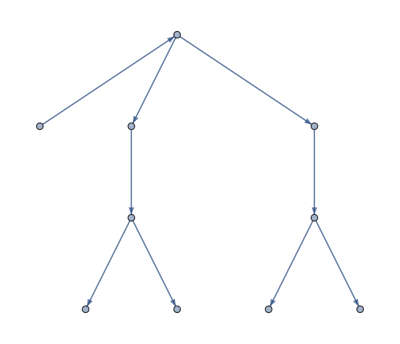
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

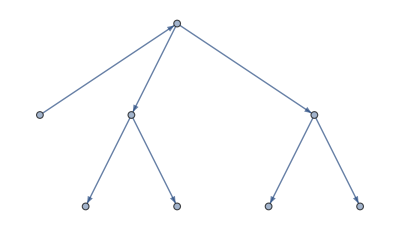
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

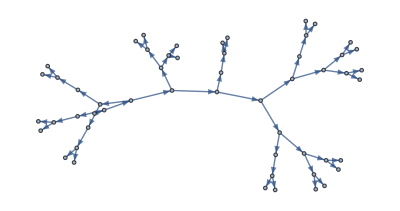
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

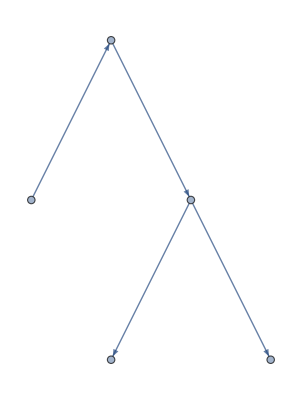
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

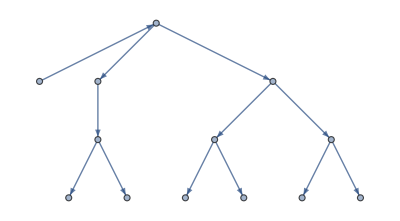
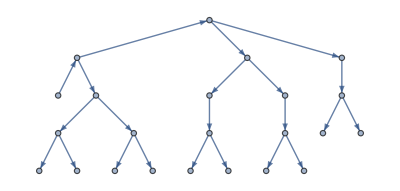
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

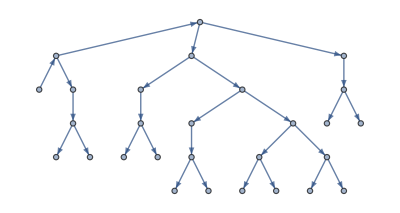
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

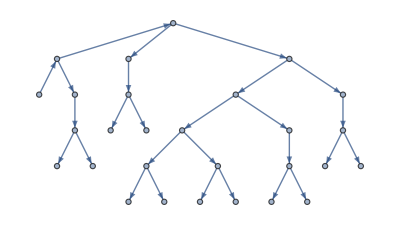
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

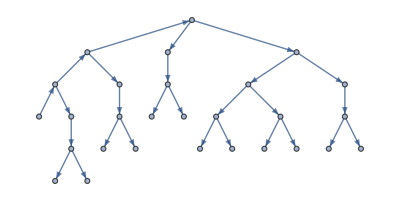
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

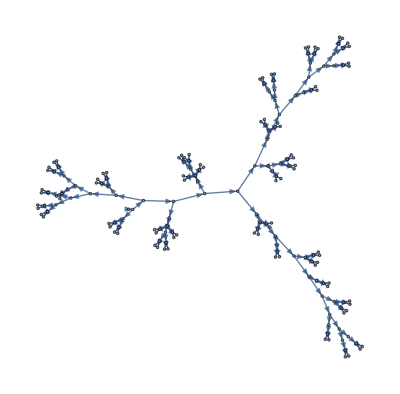
population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

population = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

«84 more identical outputs»

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

codes = {Function[x,-3.38651/x^3.38954],Function[x,-3.22124/x^3.23951],Function[x,4.9354/x^0.494115],Function[x,4.95884 x^2.50617],Function[x,2.73825/x^0.70494],Function[x,0.891879/x^0.944555],Function[x,-1.61633/x^1.49102],Function[x,3.02785/x^3.059],Function[x,-0.0616952/x^2.58772],Function[x,-0.115166 x^3.47345]}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll[init];
init = RandomDerivation[root, rulesPolynom2, {root, 1, 0}, Graph[{}]];
init = VertexDelete[init, First[Select[VertexList[init], VertexInDegree[init, #] == 0 &]]];
c[y_] := True;
res = GeneticAlgorithm[init, DerivationGraphFitness, {c}, DerivationGraphCrossover[rulesPolynom2], DerivationGraphMutation[rulesPolynom2]];
Graph[#, VertexLabels->"Name"]& /@ Last[res]
codes = CodeFromDerivation[#, rulesPolynom2]& /@ Last[res];
codes = (# //. Hold[n_]->n)& /@ codes;
Print["codes = ", codes];
Plot[{#[x], x^2-x^3} ,{x, 0, 10}]& /@ codes
```